Theory of variational quantum simulation

Xiao Yuan, Suguru Endo, Qi Zhao, Ying Li, and Simon C. Benjamin (2019)
https://quantum-journal.org/papers/q-2019-10-07-191/

Notebook: Óscar Amaro, November 2024,  @ GoLP-EPP

## Figure 2

{0.1734,0.3909}

{ⅇ^(-(ⅈ θz)/2) Cos[θx/2],-ⅈ ⅇ^((ⅈ θz)/2) Sin[θx/2]}

{2 Sin[θz[t]],0}

{{θz→Function[{t},0.3909],θx→Function[{t},0.1734+0.762041 t]}}

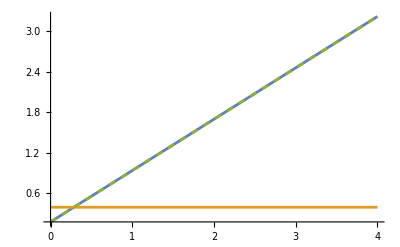

```mathematica
Clear[X,Y,Z,Rx,Rz,θx,θz,H,t,A,Ci,Cx,Cz,dθ,s]
(* Pauli terms *)
{X,Y,Z}=Table[PauliMatrix[i],{i,1,3}];
(* initial conditions *)
θ0={0.1734,0.3909}

(* rotations on wavefunction *)
Rx=MatrixExp[-I θx X/2];
Rz=MatrixExp[-I θz Z/2];
(* parametrized wavefunction *)
ψ=Rz.Rx.{1,0}
(*Hamiltonian*)
H=Y;

(* derivatives of wavefunction *)
dxψ=D[ψ,θx];
dzψ=D[ψ,θz];

(* eq 10 A_ij *)
Axx=Conjugate[dxψ].dxψ;
Axz=Conjugate[dxψ].dzψ;
Azx=Conjugate[dzψ].dxψ;
Azz=Conjugate[dzψ].dzψ;
(* eq 10 C_i *)
Cx=Conjugate[dxψ].H.ψ;
Cz=Conjugate[dzψ].H.ψ;

(* group into matrix and column *)
A={{Axx,Axz},{Azx,Azz}}//FullSimplify;
Ci={Cx,Cz}//FullSimplify;

(* take real and imag parts of A and C respectively *)
AR=Refine[Re[A],{θx>0,θz>0}];
CiI=Refine[Im[Ci],{θx>0,θz>0}];
(* eq 12 invert matrix AR to get time derivative of variational angles *)
dθ=Refine[Inverse[AR].CiI//FullSimplify,{θx>0,θz>0}];
dθ=dθ/.{θx->θx[t],θz->θz[t]}

s=DSolve[{θx'[t]==dθ[[1]],θz'[t]==dθ[[2]],θx[0]==θ0[[1]],θz[0]==θ0[[2]]},{θx,θz},t]
Plot[{Evaluate[θx[t]/.s],Evaluate[θz[t]/.s],θ0[[1]]+2 Sin[θ0[[2]]]t},{t,0,4},PlotRange->All,PlotStyle->{Default,Default,Dashed}]
```